tamoaltas - Transformada de Fourier
-Graphics-

```mathematica
(* Constantes *)
T = 4;
```

```mathematica
(* Se definen las funciones *)
f[x_]:=Cos[ (Pi x)/2]
g[x_]:=1/2(Cos[ (Pi x)/2] + Cos[ (3Pi x)/2] )
```

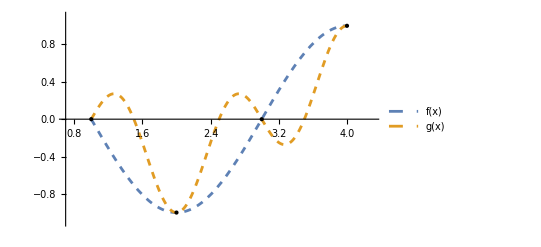

```mathematica
(* Se grafican las ondas *)
xp = (T-1)*0.1;
(* https://resources.wolframcloud.com/FunctionRepository/resources/IntersectionPlot/ *)
plot = ResourceFunction["IntersectionPlot"][{f[x],g[x]},
{x,1,T},
PlotStyle->{Dashed,Dashed},
PlotLegends->{"f(x)", "g(x)"},
PlotRange->{{1-xp,T+xp},{-1.1,1.1}}]
```

Las funciones son distintas, pero coinciden en los puntos x = 1, 2, 3, 4. Por esta razón se llegan a transformaciones de Fourier discretas idénticas.  Que la dimensión del espacio tienda a infinito equivale a tomar puntos separados por pasos infinitesimales, lo cual eliminaría cualquier ambigüedad sobre las funciones que los describen.

```mathematica
imagesDir=FileNameJoin[{NotebookDirectory[],"/images" }];
plotName= StringJoin[ {FileBaseName[NotebookFileName[]], ".png"}];
filePath= FileNameJoin[{imagesDir,plotName}];

(* Se crea el directorio si no existe *)
If[!DirectoryQ[imagesDir],CreateDirectory[imagesDir]];
```

```mathematica
Export[filePath,plot,ImageResolution->Automatic];
```